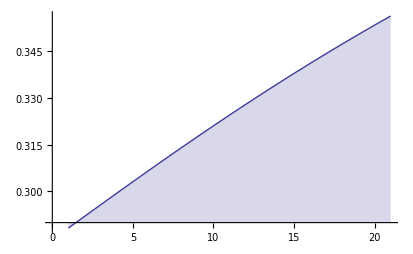

```mathematica
f[x_]:=10^-x;
ListPlot[Table[((∫_0.2^1 (Abs[f[x]])^p ⅆx)/(∫_0.2^1 1ⅆx))^(1/p),{p,1,3,0.1}],Joined->True,Filling->Axis,PlotRange->Full]
```